# Supporting Mathematica File for Reciprocal Preferences and Expectations in International Agreements

The number of countries is denoted by “n” instead of “N” here, as the capital N is a command in Mathematica.

## Signatory and Non-signatory Efforts

Non-signatory i’s best-response function

```mathematica
qni[b_,c_,n_,k_,α_,η_,qqs_]:=(b(n-1)+α(k qqs-(n-1)η))/(c(n-1)-α(n-k-1))
```

Signatories’ objective function

```mathematica
Us[b_,c_,n_,k_,α_,η_,qqs_,qqn_]:=b(k qqs+(n-k)qqn)-(c/2)qqs^2+α(((k-1)qqs+(n-k)qqn)/(n-1) -η )(qqs+1-η)
```

Taking derivative of Us wrt a signatory’s effort, equating it to zero, and finally solving for a signatory’s effort yields

```mathematica
Solve[D[Us[b,c,n,k,α,η,qqs,qni[b,c,n,k,α,η,qqs]],qqs]==0,qqs]
```

{{qqs→(-(b (-k+n) α)/(c (-1+n)-(-1-k+n) α)-(α (-1+k+(k (-k+n) α)/(c (-1+n)-(-1-k+n) α)))/(-1+n)-b (k+(k (-k+n) α)/(c (-1+n)-(-1-k+n) α))+α η+((-k+n) α^2 η)/(c (-1+n)-(-1-k+n) α)+(α (-1+k+(k (-k+n) α)/(c (-1+n)-(-1-k+n) α)) η)/(-1+n))/(-c+((-1+k) α)/(-1+n)+(k (-k+n) α^2)/((-1+n) (c (-1+n)-(-1-k+n) α))+(α (-1+k+(k (-k+n) α)/(c (-1+n)-(-1-k+n) α)))/(-1+n))}}

Signatory effort - Equation (17):

```mathematica
qs[b_,c_,n_,k_,α_,η_]=FullSimplify[(-(b (-k+n) α)/(c (-1+n)-(-1-k+n) α)-(α (-1+k+(k (-k+n) α)/(c (-1+n)-(-1-k+n) α)))/(-1+n)-b (k+(k (-k+n) α)/(c (-1+n)-(-1-k+n) α))+α η+((-k+n) α^2 η)/(c (-1+n)-(-1-k+n) α)+(α (-1+k+(k (-k+n) α)/(c (-1+n)-(-1-k+n) α)) η)/(-1+n))/(-c+((-1+k) α)/(-1+n)+(k (-k+n) α^2)/((-1+n) (c (-1+n)-(-1-k+n) α))+(α (-1+k+(k (-k+n) α)/(c (-1+n)-(-1-k+n) α)))/(-1+n))]
```

(b c k (-1+n)+b n α+α (α-2 α η+c (-1+k-(-2+k+n) η)))/(c^2 (-1+n)-c (-3+k+n) α-2 α^2)

Non-signatory effort - Equation (18):

```mathematica
qn[b_,c_,n_,k_,α_,η_]=FullSimplify[qni[b,c,n,k,α,η,qs[b,c,n,k,α,η]]]
```

(b (-1+n)-(-1+n) α η+(k α (b c k (-1+n)+b n α+α (α-2 α η+c (-1+k-(-2+k+n) η))))/(c^2 (-1+n)-c (-3+k+n) α-2 α^2))/(c (-1+n)+(1+k-n) α)

## Proposition 2

Equation (A8):

Taking derivative of signatory’s effort wrt to k:

```mathematica
FullSimplify[D[qs[b,c,n,k,α,η],k]]
```

(c (c (-1+n)+α) (b c (-1+n)-b (-2+n) α-α (α+c (-1+η))))/((-c^2 (-1+n)+c (-3+k+n) α+2 α^2)^2)

A supporting Figure of how signatory and non-signatory efforts change in k below. The formal proof is in the paper.

```mathematica
Manipulate[Plot[{qn[0.25,1,10,k,0.1,η],qs[0.25,1,10,k,0.1,η]},{k,1,10}],{η,0,1}]
```

The following difference is used in the proof of proposition 2(2) as equation (A9):

```mathematica
FullSimplify[qs[b,c,n,k,α,η]-qn[b,c,n,k,α,η]]
```

((-1+n) (c (-1+k)+α) (b c (-1+n)-b (-2+n) α-α (α+c (-1+η))))/((c (-1+n)+(1+k-n) α) (c^2 (-1+n)-c (-3+k+n) α-2 α^2))

## Proposition 3

Notation: we use “a” for “α” lower bar to conveniently type it on Mathematica.
Let’s start with the signatory effort:

```mathematica
qsa[b_,c_,n_,k_,a_,η_]:=qs[b,c,n,k,(a c)/(c-b),η]
```

Taking derivative of signatory effort wrt a:

```mathematica
Dqsaa[b_,c_,n_,k_,a_,η_]=FullSimplify[D[qsa[b,c,n,k,a,η],a]]
```

-((b-c) (a^2 (2 b n+c (1+k-n-2 η))-2 a (b-c) (-1+n) (c+2 b k-2 c η)+(b-c)^2 (-1+n) (b (n+k (-3+k+n))+c (-1+k-(-2+k+n) η))))/(c (-2 a^2+(b-c)^2 (-1+n)+a (b-c) (-3+k+n))^2)

```mathematica
-(((b-c) (a^2 (2 b n+c (1+k-n-2 η))-2 a (b-c) (-1+n) (c+2 b k-2 c η)+(b-c)^2 (-1+n) (b (n+k (-3+k+n))+c (-1+k-(-2+k+n) η))))/(c (-2 a^2+(b-c)^2 (-1+n)+a (b-c) (-3+k+n))^2))
```

-((b-c) (a^2 (2 b n+c (1+k-n-2 η))-2 a (b-c) (-1+n) (c+2 b k-2 c η)+(b-c)^2 (-1+n) (b (n+k (-3+k+n))+c (-1+k-(-2+k+n) η))))/(c (-2 a^2+(b-c)^2 (-1+n)+a (b-c) (-3+k+n))^2)

Evaluating at a=0:

```mathematica
FullSimplify[Dqsaa[b,c,n,k,0,η]]
```

-(b (n+k (-3+k+n))+c (-1+k-(-2+k+n) η))/((b-c) c (-1+n))

Solving for the critical eta threshold, yields T_H:

```mathematica
FullSimplify[Solve[b (n+k (-3+k+n))+c (-1+k-(-2+k+n) η)==0,η]]
```

{{η→(c (-1+k)+b (n+k (-3+k+n)))/(c (-2+k+n))}}

Non-signatory effort:

```mathematica
qna[b_,c_,n_,k_,a_,η_]:=FullSimplify[qn[b,c,n,k,(a c)/(c-b),η]]
```

Derivative wrt a:

```mathematica
Dqnaa[b_,c_,n_,k_,a_,η_]=FullSimplify[D[qna[b,c,n,k,a,η],a]]
```

(((-1+(a (1+k-n))/(-b+c)+n) (c (-1+n) η+(a k (2 a c (-1+2 η)+(b-c) (b n+c (-1+k-(-2+k+n) η))))/(-2 a^2+(b-c)^2 (-1+n)+a (b-c) (-3+k+n))-(a k (-4 a+(b-c) (-3+k+n)) (-b (b-c)^2 k (-1+n)+a^2 c (-1+2 η)+a (b-c) (b n+c (-1+k-(-2+k+n) η))))/((-2 a^2+(b-c)^2 (-1+n)+a (b-c) (-3+k+n))^2)+(k (-b (b-c)^2 k (-1+n)+a^2 c (-1+2 η)+a (b-c) (b n+c (-1+k-(-2+k+n) η))))/(-2 a^2+(b-c)^2 (-1+n)+a (b-c) (-3+k+n))))/(b-c)-((1+k-n) (b (-1+n)+(a c (-1+n) η)/(b-c)+(a k (-b (b-c)^2 k (-1+n)+a^2 c (-1+2 η)+a (b-c) (b n+c (-1+k-(-2+k+n) η))))/((b-c) (-2 a^2+(b-c)^2 (-1+n)+a (b-c) (-3+k+n)))))/(-b+c))/(c (-1+(a (1+k-n))/(-b+c)+n)^2)

Evaluating at a=0:

```mathematica
FullSimplify[Dqnaa[b,c,n,k,0,η]]
```

(b (-1+(-1+k) k+n)-c (-1+n) η)/(c (-b+c) (-1+n))

Solving for the critical eta threshold, yields T_L:

```mathematica
FullSimplify[Solve[(b (-1+(-1+k) k+n)-c (-1+n) η)/(c (-b+c) (-1+n))==0,η]]
```

{{η→(b (-1+(-1+k) k+n))/(c (-1+n))}}

T_H - T_L:

```mathematica
diff[b_,c_,k_,n_]=FullSimplify[(c (-1+k)+b (n+k (-3+k+n)))/(c (-2+k+n))-(b (-1+(-1+k) k+n))/(c (-1+n))]
```

(b k-(b (-1+k) k)/(-1+n)-((2 b-c) (-1+k))/(-2+k+n))/c

For the boundary of T_H:

```mathematica
FullSimplify[Solve[k(n+k-3)-n(n-2)==0,k]]
```

{{k→1/2 (3-n-√((-1+n) (-9+5 n)))},{k→1/2 (3-n+√((-1+n) (-9+5 n)))}}

For n=100, the smallest integer above the higher of the two numbers above shows for k > 62, we have T_H >1:

```mathematica
Ceiling[1/2 (3-100+√((-1+100) (-9+5 100)))]
```

62

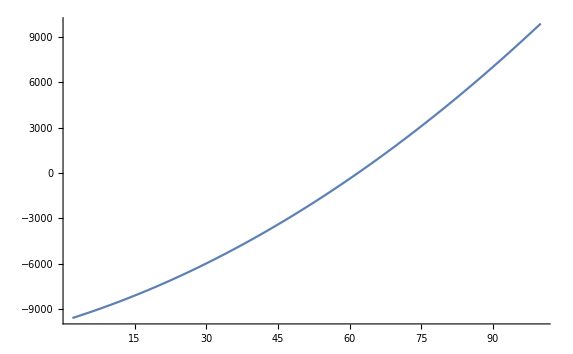

```mathematica
Plot[k(100+k-3)-100(100-2),{k,2,100}]
```

## Indirect Utility Functions with alpha

We omit writing these indirect utility functions omitted in the paper due to their size and complexity. 
Signatory

```mathematica
FullSimplify[Us[b,c,n,k,α,η,qs[b,c,n,k,α,η],qn[b,c,n,k,α,η]]]
```

1/(2 (c (-1+n)+(1+k-n) α) (c^2 (-1+n)-c (-3+k+n) α-2 α^2))(b^2 (c^2 (-1+n)^2 ((-2+k) k+2 n)+2 c (-1+n) (k^2+k (-3+n)-(-3+n) n) α+(4 k (-1+n)+(4-3 n) n) α^2)+2 b α ((c (-1+n)+α) (c ((-2+k) k+n)+(2 k-n) α)+(-c^2 (-1+n) ((-2+k) k+n^2)+c (2 k-k^2 n+n (2+(-4+n) n)) α+2 n (-1-k+n) α^2) η)+α (α^3+2 c^3 (-1+n)^2 (-1+η) η+2 c α^2 (-1+k (-1+η)^2+η (-1+2 n+η-n η))+c^2 α (1-2 k (-1+η)^2+k^2 (-1+η)^2+η (4+2 (-4+n) n-(4+(-6+n) n) η))))

Non-signatory

```mathematica
Un[b_,c_,n_,k_,α_,η_,qqs_,qqn_]=b(k qqs+(n-k)qqn)-(c/2)qqn^2+α((k qqs+(n-k-1)qqn)/(n-1) -η )(qqn+1-η)
```

-(c qqn^2)/2+b ((-k+n) qqn+k qqs)+α (1+qqn-η) (((-1-k+n) qqn+k qqs)/(-1+n)-η)

```mathematica
FullSimplify[Un[b,c,n,k,α,η,qs[b,c,n,k,α,η],qn[b,c,n,k,α,η]]]
```

(α (b (c^2 (-1+n)^2+c (3+(-1+k) k-n) (-1+n) α+(2+(-2+k) n) α^2)-(c^2 (-1+n)^2-c (-3+n) (-1+n) α+(2+k-2 n) α^2) (α+c (-1+η))) (b (c^2 (-1+n) (-1+(-1+k) k+n)+c (-3-2 k+k^2+(4+k) n-n^2) α+2 (1+k-n) α^2)+c (-c^2 (-1+n)^2 η+α^2 (k-2 (1+k-n) η)+c α ((-1+k) k+(3+k-k^2-4 n+n^2) η))))/((c (-1+n)+(1+k-n) α)^2 (-c^2 (-1+n)+c (-3+k+n) α+2 α^2)^2)-(c (b (-1+n)-(-1+n) α η+(k α (b c k (-1+n)+b n α+α (α-2 α η+c (-1+k-(-2+k+n) η))))/(c^2 (-1+n)-c (-3+k+n) α-2 α^2))^2)/(2 (c (-1+n)+(1+k-n) α)^2)+b ((k (b c k (-1+n)+b n α+α (α-2 α η+c (-1+k-(-2+k+n) η))))/(c^2 (-1+n)-c (-3+k+n) α-2 α^2)+((-k+n) (b (-1+n)-(-1+n) α η+(k α (b c k (-1+n)+b n α+α (α-2 α η+c (-1+k-(-2+k+n) η))))/(c^2 (-1+n)-c (-3+k+n) α-2 α^2)))/(c (-1+n)+(1+k-n) α))

Self-interested non-signatory and signatory:

```mathematica
SelfUn[b_,c_,n_,k_]=FullSimplify[Un[b,c,n,k,0,η,qs[b,c,n,k,0,η],qn[b,c,n,k,0,η]]]
SelfUs[b_,c_,n_,k_]=FullSimplify[Us[b,c,n,k,0,η,qs[b,c,n,k,0,η],qn[b,c,n,k,0,η]]]
```

(b^2 (-1+2 (-1+k) k+2 n))/(2 c)

(b^2 ((-2+k) k+2 n))/(2 c)

Stable coalition size for self-interested:

```mathematica
FullSimplify[Solve[SelfUs[b,c,n,k]-SelfUn[b,c,n,k-1]==0,k]]
```

{{k→1},{k→3}}

## Lemma 1

The partial derivative of signatory indirect welfare with respect to k:

```mathematica
FullSimplify[D[Us[b,c,n,k,α,η,qs[b,c,n,k,α,η],qn[b,c,n,k,α,η]],k]]
```

((c (-1+k)+α) (c (-1+n)+α)^2 (b (c-c n+(-2+n) α)+α (α+c (-1+η)))^2)/((c (-1+n)+(1+k-n) α)^2 (-c^2 (-1+n)+c (-3+k+n) α+2 α^2)^2)

Coalition size minimizing signatory’s indirect welfare:

```mathematica
FullSimplify[Solve[D[Us[b,c,n,k,α,η,qs[b,c,n,k,α,η],qn[b,c,n,k,α,η]],k]==0,k]]
```

{{k→1-α/c}}

are used in the proof of parts (1 and 2).
At what k signatory and non-signatory indirect welfare are equal?

```mathematica
FullSimplify[Solve[Us[b,c,n,k,α,η,qs[b,c,n,k,α,η],qn[b,c,n,k,α,η]]-Un[b,c,n,k,α,η,qs[b,c,n,k,α,η],qn[b,c,n,k,α,η]]==0,k]]
```

{{k→1-α/c},{k→-((-1+n) (c-α) (c (-1+n)+2 α))/(c^2 (-1+n)^2+2 c (-1+n) α+2 α^2)}}

The latter is negative. So, they are equal at k = 1 - α/c. This proves the part 4 and it is useful to prove the parts 3 and 5.

Next, we study (Un - Us)/(k-1 + α/c):

```mathematica
FullSimplify[(Un[b,c,n,k,α,η,qs[b,c,n,k,α,η],qn[b,c,n,k,α,η]]-Us[b,c,n,k,α,η,qs[b,c,n,k,α,η],qn[b,c,n,k,α,η]])/(k-1 + α/c)]
```

(c (c^2 (1+k) (-1+n)^2+c (3+2 k-n) (-1+n) α+2 (1+k-n) α^2) (b (c-c n+(-2+n) α)+α (α+c (-1+η)))^2)/(2 (c (-1+n)+(1+k-n) α)^2 (-c^2 (-1+n)+c (-3+k+n) α+2 α^2)^2)

For this term to be positive, the first term in the numerator has to be positive since the rest of the terms are non-zero and squared.

```mathematica
termunus[c_,n_,k_,α_]=c^2 (1+k) (-1+n)^2+c (3+2 k-n) (-1+n) α+2 (1+k-n) α^2
```

c^2 (1+k) (-1+n)^2+c (3+2 k-n) (-1+n) α+2 (1+k-n) α^2

Does this term increase in c?

```mathematica
FullSimplify[D[termunus[c,n,k,α],c]]
```

(-1+n) (2 c (1+k) (-1+n)+(3+2 k-n) α)

```mathematica
FullSimplify[(-1+n) (4 α (1+k) (-1+n)+(3+2 k-n) α)]
```

(-1+n) (-1+3 n+k (-2+4 n)) α

```mathematica
FullSimplify[termunus[2α,n,k,α]]
```

2 (k+(-1+n) n+2 k (-1+n) n) α^2

### Lemma 2

Let us start with the U_s.
The partial derivative of signatory indirect utility wrt qn

```mathematica
D[Us[b,c,n,k,(a c)/(c-b),η,qs,qn],qn]
```

b (-k+n)+(a c (-k+n) (1+qs-η))/((-b+c) (-1+n))

The partial derivative of non-signatory effort wrt a

```mathematica
FullSimplify[D[qn[b,c,n,k,(a c)/(c-b),η],a]]
```

1/((b-c) c (-1+(a (1+k-n))/(-b+c)+n)^2 (-2 a^2+(b-c)^2 (-1+n)+a (b-c) (-3+k+n))^2)(a^4 (-2 b (1+k-n) (2+(-2+k) n)-c k (3+2 k+k^2-2 (2+k) n+n^2)+2 c (2+k-2 n) (1+k-n) η)+4 a^3 (b-c) (-1+n) (-c k (-2+n)+b (3+2 k+k^3-(4+k^2) n+n^2)+c (1+k-n) (-3+n) η)-(b-c)^4 (-1+n)^3 (b (-1+(-1+k) k+n)-c (-1+n) η)-a^2 (b-c)^2 (-1+n) (c k (-7-2 k (-2+n)+5 n)+b (-13-7 k+(-3+k) k^3+23 n+k (6+5 k) n-(11+k+k^2) n^2+n^3)+c (k (8-6 n)+k^2 (-3+n)-(-1+n) (13+(-10+n) n)) η)+2 a (b-c)^3 (-1+n)^2 (b (-3-2 k+k^2+(4+k) n-n^2)+c ((-1+k) k+(3+k-k^2-4 n+n^2) η)))

The partial derivative of signatory indirect utility wrt qn (qs at optimal) times the partial derivative of non-signatory effort wrt a

```mathematica
derUsqna[b_,c_,n_,k_,a_,η_]:=FullSimplify[(b (-k+n)+(a c (-k+n) (1+qs[b,c,n,k,(a c)/(c-b),η]-η))/((-b+c) (-1+n)))((a^4 (-2 b (1+k-n) (2+(-2+k) n)-c k (3+2 k+k^2-2 (2+k) n+n^2)+2 c (2+k-2 n) (1+k-n) η)+4 a^3 (b-c) (-1+n) (-c k (-2+n)+b (3+2 k+k^3-(4+k^2) n+n^2)+c (1+k-n) (-3+n) η)-(b-c)^4 (-1+n)^3 (b (-1+(-1+k) k+n)-c (-1+n) η)-a^2 (b-c)^2 (-1+n) (c k (-7-2 k (-2+n)+5 n)+b (-13-7 k+(-3+k) k^3+23 n+k (6+5 k) n-(11+k+k^2) n^2+n^3)+c (k (8-6 n)+k^2 (-3+n)-(-1+n) (13+(-10+n) n)) η)+2 a (b-c)^3 (-1+n)^2 (b (-3-2 k+k^2+(4+k) n-n^2)+c ((-1+k) k+(3+k-k^2-4 n+n^2) η)))/((b-c) c (-1+(a (1+k-n))/(-b+c)+n)^2 (-2 a^2+(b-c)^2 (-1+n)+a (b-c) (-3+k+n))^2))]
```

Evaluating at alpha = 0.

```mathematica
FullSimplify[derUsqna[b,c,n,k,0,η]]
```

(b (k-n) (b (-1+(-1+k) k+n)-c (-1+n) η))/((b-c) c (-1+n))

The partial derivative of signatory indirect utility wrt qs

```mathematica
D[Us[b,c,n,k,(a c)/(c-b),η,qs,qn],qs]
```

b k-c qs+(a c (-1+k) (1+qs-η))/((-b+c) (-1+n))+(a c (((-k+n) qn+(-1+k) qs)/(-1+n)-η))/(-b+c)

The partial derivative of signatory effort wrt a

```mathematica
FullSimplify[D[qs[b,c,n,k,(a c)/(c-b),η],a]]
```

-((b-c) (a^2 (2 b n+c (1+k-n-2 η))-2 a (b-c) (-1+n) (c+2 b k-2 c η)+(b-c)^2 (-1+n) (b (n+k (-3+k+n))+c (-1+k-(-2+k+n) η))))/(c (-2 a^2+(b-c)^2 (-1+n)+a (b-c) (-3+k+n))^2)

The partial derivative of signatory indirect utility wrt qs (qs and qn at optimal) times t partial derivative of signatory effort wrt a

```mathematica
derUsqsa[b_,c_,n_,k_,a_,η_]:=FullSimplify[(b k-c (qs[b,c,n,k,(a c)/(c-b),η])+(a c (-1+k) (1+(qs[b,c,n,k,(a c)/(c-b),η])-η))/((-b+c) (-1+n))+(a c (((-k+n) (qn[b,c,n,k,(a c)/(c-b),η])+(-1+k) (qs[b,c,n,k,(a c)/(c-b),η]))/(-1+n)-η))/(-b+c))(-(((b-c) (a^2 (2 b n+c (1+k-n-2 η))-2 a (b-c) (-1+n) (c+2 b k-2 c η)+(b-c)^2 (-1+n) (b (n+k (-3+k+n))+c (-1+k-(-2+k+n) η))))/(c (-2 a^2+(b-c)^2 (-1+n)+a (b-c) (-3+k+n))^2)))]
```

```mathematica
FullSimplify[derUsqsa[b,c,n,k,0,η]]
```

0

Combining both:

```mathematica
derUsazero[b_,c_,n_,k_,η_]=FullSimplify[derUsqna[b,c,n,k,0,η]+derUsqsa[b,c,n,k,0,η]]
```

(b (k-n) (b (-1+(-1+k) k+n)-c (-1+n) η))/((b-c) c (-1+n))

Finding the critical level of eta that equate the term above to zero:

```mathematica
FullSimplify[Solve[derUsazero[b,c,n,k,η]==0,η]]
```

{{η→(b (-1+(-1+k) k+n))/(c (-1+n))}}

which is identical to T_L and completes the part 1, see equation (A12) in the paper.

Let us continue with the U_n.
The partial derivative of non-signatory indirect utility wrt qs

```mathematica
D[Un[b,c,n,k,(a c)/(c-b),η,qs,qn],qs]
```

b k+(a c k (1+qn-η))/((-b+c) (-1+n))

The partial derivative of signatory effort wrt a

```mathematica
FullSimplify[D[qs[b,c,n,k,(a c)/(c-b),η],a]]
```

-((b-c) (a^2 (2 b n+c (1+k-n-2 η))-2 a (b-c) (-1+n) (c+2 b k-2 c η)+(b-c)^2 (-1+n) (b (n+k (-3+k+n))+c (-1+k-(-2+k+n) η))))/(c (-2 a^2+(b-c)^2 (-1+n)+a (b-c) (-3+k+n))^2)

The partial derivative of non-signatory indirect utility wrt qs (qn at optimal) times the partial derivative of signatory effort wrt alpha

```mathematica
derUnqsa[b_,c_,n_,k_,a_,η_]:=FullSimplify[(b k+(a c k (1+(qn[b,c,n,k,(a c)/(c-b),η])-η))/((-b+c) (-1+n)))(-(((b-c) (a^2 (2 b n+c (1+k-n-2 η))-2 a (b-c) (-1+n) (c+2 b k-2 c η)+(b-c)^2 (-1+n) (b (n+k (-3+k+n))+c (-1+k-(-2+k+n) η))))/(c (-2 a^2+(b-c)^2 (-1+n)+a (b-c) (-3+k+n))^2)))]
```

Evaluating at alpha = 0.

```mathematica
FullSimplify[derUnqsa[b,c,n,k,0,η]]
```

-(b k (b (n+k (-3+k+n))+c (-1+k-(-2+k+n) η)))/((b-c) c (-1+n))

The partial derivative of non-signatory indirect utility wrt qn

```mathematica
FullSimplify[D[Un[b,c,n,k,(a c)/(c-b),η,qs,qn],qn]]
```

b (-k+n)-c qn+(a c (-(-1+n) (1+2 qn-2 η)+k (1+2 qn-qs-η)))/((b-c) (-1+n))

The partial derivative of non-signatory effort wrt a

```mathematica
FullSimplify[D[qn[b,c,n,k,(a c)/(c-b),η],a]]
```

1/((b-c) c (-1+(a (1+k-n))/(-b+c)+n)^2 (-2 a^2+(b-c)^2 (-1+n)+a (b-c) (-3+k+n))^2)(a^4 (-2 b (1+k-n) (2+(-2+k) n)-c k (3+2 k+k^2-2 (2+k) n+n^2)+2 c (2+k-2 n) (1+k-n) η)+4 a^3 (b-c) (-1+n) (-c k (-2+n)+b (3+2 k+k^3-(4+k^2) n+n^2)+c (1+k-n) (-3+n) η)-(b-c)^4 (-1+n)^3 (b (-1+(-1+k) k+n)-c (-1+n) η)-a^2 (b-c)^2 (-1+n) (c k (-7-2 k (-2+n)+5 n)+b (-13-7 k+(-3+k) k^3+23 n+k (6+5 k) n-(11+k+k^2) n^2+n^3)+c (k (8-6 n)+k^2 (-3+n)-(-1+n) (13+(-10+n) n)) η)+2 a (b-c)^3 (-1+n)^2 (b (-3-2 k+k^2+(4+k) n-n^2)+c ((-1+k) k+(3+k-k^2-4 n+n^2) η)))

The partial derivative of non-signatory indirect utility wrt qn times the partial derivative of non-signatory effort wrt a

```mathematica
derUnqna[b_,c_,n_,k_,a_,η_]:=FullSimplify[(b (-k+n)-c (qn[b,c,n,k,(a c)/(c-b),η])+1/((b-c) (-1+n))a c (-(-1+n) (1+2 (qn[b,c,n,k,(a c)/(c-b),η])-2 η)+k (1+2 (qn[b,c,n,k,(a c)/(c-b),η])-(qs[b,c,n,k,(a c)/(c-b),η])-η)))((a^4 (-2 b (1+k-n) (2+(-2+k) n)-c k (3+2 k+k^2-2 (2+k) n+n^2)+2 c (2+k-2 n) (1+k-n) η)+4 a^3 (b-c) (-1+n) (-c k (-2+n)+b (3+2 k+k^3-(4+k^2) n+n^2)+c (1+k-n) (-3+n) η)-(b-c)^4 (-1+n)^3 (b (-1+(-1+k) k+n)-c (-1+n) η)-a^2 (b-c)^2 (-1+n) (c k (-7-2 k (-2+n)+5 n)+b (-13-7 k+(-3+k) k^3+23 n+k (6+5 k) n-(11+k+k^2) n^2+n^3)+c (k (8-6 n)+k^2 (-3+n)-(-1+n) (13+(-10+n) n)) η)+2 a (b-c)^3 (-1+n)^2 (b (-3-2 k+k^2+(4+k) n-n^2)+c ((-1+k) k+(3+k-k^2-4 n+n^2) η)))/((b-c) c (-1+(a (1+k-n))/(-b+c)+n)^2 (-2 a^2+(b-c)^2 (-1+n)+a (b-c) (-3+k+n))^2))]
```

Evaluating at alpha = 0.

```mathematica
FullSimplify[derUnqna[b,c,n,k,0,η]]
```

(b (1+k-n) (b (-1+(-1+k) k+n)-c (-1+n) η))/((b-c) c (-1+n))

Combining both:

```mathematica
derUnazero[b_,c_,n_,k_,η_]=FullSimplify[derUnqsa[b,c,n,k,0,η]+derUnqna[b,c,n,k,0,η]]
```

(b (-b (-k (-2+n)+(-1+n)^2+k^2 (-3+2 n))+c (k+k^2 (-1+η)-k η+(-1+n)^2 η)))/((b-c) c (-1+n))

```mathematica
FullSimplify[Solve[derUnazero[b,c,n,k,η]==0,η]]
```

{{η→(c (-1+k) k+b (-k (-2+n)+(-1+n)^2+k^2 (-3+2 n)))/(c ((-1+k) k+(-1+n)^2))}}

which we call T_{U_{ns}} in the paper in equation (A13), completing part 2.

The partial derivative of non-signatory indirect welfare wrt a at k-1 and evaluating at a = 0:

```mathematica
FullSimplify[derUnazero[b,c,n,k-1,η]]
```

(b (-c (-2+k) (-1+k)-b (-4+(8-3 k) k+n+k (-5+2 k) n+n^2)+c (3+(-3+k) k+(-2+n) n) η))/((b-c) c (-1+n))

```mathematica
FullSimplify[Solve[derUnazero[b,c,n,k-1,η]==0,η]]
```

{{η→(c (-2+k) (-1+k)+b (-4+(8-3 k) k+n+k (-5+2 k) n+n^2))/(c (3+(-3+k) k+(-2+n) n))}}

which we call T_{U_{ns}(k-1)} in the paper in equation (A14), completing part 3.

Let us compare these three thresholds, starting with T_Uns -T_L:

```mathematica
FullSimplify[(c (-1+k) k+b (-k (-2+n)+(-1+n)^2+k^2 (-3+2 n)))/(c ((-1+k) k+(-1+n)^2))-(b (-1+(-1+k) k+n))/(c (-1+n))]
```

(k (2 b (-1+n)+c (-1+k) (-1+n)+b k (2-(-2+k) k+(-4+n) n)))/(c ((-1+k) k+(-1+n)^2) (-1+n))

T_Uns(k) - T_Uns(k-1):

```mathematica
FullSimplify[(c (-1+k) k+b (-k (-2+n)+(-1+n)^2+k^2 (-3+2 n)))/(c ((-1+k) k+(-1+n)^2))-(c (-2+k) (-1+k)+b (-4+(8-3 k) k+n+k (-5+2 k) n+n^2))/(c (3+(-3+k) k+(-2+n) n))]
```

((-1+n) (2 c (-1+k) (-1+n)-b (k^2-k (3-2 n)^2+(-1+n) (-7+3 n))))/(c ((-1+k) k+(-1+n)^2) (3+(-3+k) k+(-2+n) n))

For this term to be positive, we need 2 c (-1+k) (-1+n)-b (k^2-k (3-2 n)^2+(-1+n) (-7+3 n))>0. Taking the term starting with -b to the RHS, leaving b/c on the RHS, multiplying both sides with n yields the following since bn/c=1:

```mathematica
FullSimplify[2  (-1+k) (-1+n)-(k^2-k (3-2 n)^2+(-1+n) (-7+3 n))>0]
```

(8-3 n) n+k (7+2 n (-5+2 n))>5+k^2

T_L - T_Uns(k-1):

```mathematica
FullSimplify[(b (-1+(-1+k) k+n))/(c (-1+n))-(c (-2+k) (-1+k)+b (-4+(8-3 k) k+n+k (-5+2 k) n+n^2))/(c (3+(-3+k) k+(-2+n) n))]
```

((-1+k) (-c (-2+k) (-1+n)+b (7+k (-1+(-3+k) k)-10 n+4 k n-(-3+k) n^2)))/(c (-1+n) (3+(-3+k) k+(-2+n) n))

Another simplification

```mathematica
FullSimplify[(7+k (-1+(-3+k) k)-10 n+4 k n-(-3+k) n^2)>n(-2+k) (-1+n)]
```

7+k (-1+(-3+k) k)+5 k n+(5-2 k) n^2>12 n

```mathematica
differencea[k_,n_]:=n^2(5-2k)+n(5k-12)+k(k-3)+7
```

Manipulating the parameter values of k reveals that this term is positive for k ≤ 2 and negative for k ≥3.

```mathematica
Manipulate[Plot[differencea[k,n],{n,3,100}],{k,1,100}]
```

### Understanding Boundaries of Thresholds: [b/c , 1]

T_{U_{ns}} = (c (-1+k) k+b (-k (-2+n)+(-1+n)^2+k^2 (-3+2 n)))/(c ((-1+k) k+(-1+n)^2)).

For T_{U_{ns}} < 1, we found the following equivalent condition in the paper: (n-1)^3 - k^2 (2n-3) + k(n-2) > 0
Numerically analyzing it shows that the condition does not hold for sufficiently high k relative to n:

```mathematica
cond[k_,n_]:=(n-1)^3-k^2 (2n-3)+k(n-2)
```

```mathematica
cond[6,10]
```

165

```mathematica
cond[7,10]
```

-48

The condition T_{U_{ns}(k-1)} = (c (-2+k) (-1+k)+b (-4+(8-3 k) k+n+k (-5+2 k) n+n^2))/(c (3+(-3+k) k+(-2+n) n)) > b/c is equivalent to

```mathematica
FullSimplify[n^2+k n(2k-5)+n+k(8-3k)-4>n(n-2)+k(k-3)+3-n(k-2)(k-1)]
```

(-1+k) (7-5 n+k (-4+3 n))>0

```mathematica
conk[k_,n_]:=7-5 n+k (-4+3 n)
```

```mathematica
conk[1,10]
```

-17

```mathematica
conk[2,10]
```

9

We found that _{U_{ns}(k-1)}  < 1 is equivalent to:

```mathematica
cont[k_,n_]:=n^2(n-3)+n(5k+4)-k^2 (2n-3)-8k
```

```mathematica
cont[7,10]
```

201

```mathematica
cont[8,10]
```

-12

## Proposition 4

```mathematica
FullSimplify[derUsazero[b,c,n,3,η]]
```

(b (3-n) (b (5+n)-c (-1+n) η))/((b-c) c (-1+n))

```mathematica
FullSimplify[derUnazero[b,c,n,2,η]]
```

(b (7 b-2 c-b n (4+n)+c (3+(-2+n) n) η))/((b-c) c (-1+n))

```mathematica
FullSimplify[b (3-n) (b (5+n)-c (-1+n) η)>b (7 b-2 c-b n (4+n)+c (3+(-2+n) n) η)]
```

b (c+b (4+n)-c n η)>0

We solved for η in the paper and find that coalition size contracts at η < (2N+4)/N^2 under small alpha assumption.
We call this threshold T_2, since the coalition size contracts to 2. 

T_2 > T_{U_{ns}(k-1)} if 
(2n+4)/n^2>(c (-2+k) (-1+k)+b (-4+(8-3 k) k+n+k (-5+2 k) n+n^2))/(c (3+(-3+k) k+(-2+n) n))
Getting rid of the b and c as usual using bn/c = 1, we get the following:

```mathematica
FullSimplify[(2n+4)/n-(n(k-2)(k-1))/(3+(-3+k) k+(-2+n) n) > (-4+(8-3 k) k+n+k (-5+2 k) n+n^2)/(3+(-3+k) k+(-2+n) n)]
```

2+4/n>((-1+n) (4+k (-8+3 k)+n))/(3+(-3+k) k+(-2+n) n)

```mathematica
term2[k_,n_]:=2+4/n-((-1+n) (4+k (-8+3 k)+n))/(3+(-3+k) k+(-2+n) n)
```

Around k = 3

```mathematica
term2[3,n]
```

2+4/n-((-1+n) (7+n))/(3+(-2+n) n)

The term above is used for the equation (A14) in the paper.

T_2 > T_{U_{ns}} if
 (2n+4)/n^2>(c (-1+k) k+b (-k (-2+n)+(-1+n)^2+k^2 (-3+2 n)))/(c ((-1+k) k+(-1+n)^2))

Getting rid of the b and c as usual using bn/c = 1, we get the following:

```mathematica
FullSimplify[(2n+4)/n- (n k (k-1))/(k(k-1) + (n-1)^2) > (-k (-2+n)+(-1+n)^2+k^2 (-3+2 n))/((-1+k) k+(-1+n)^2)]
```

2+4/n>((-1+n) (-1+k (-2+3 k)+n))/((-1+k) k+(-1+n)^2)

```mathematica
term3[k_,n_]:=FullSimplify[2+4/n-((-1+n) (-1+k (-2+3 k)+n))/((-1+k) k+(-1+n)^2)]
```

Around k = 3

```mathematica
Factor[term3[3,n]]
```

(28+26 n-19 n^2+n^3)/(n (7-2 n+n^2))

The terms above are used in equation (A16) and in the previous inequality in the paper.

```mathematica
term3[3,18]
```

86/2655

```mathematica
term3[3,17]
```

-54/2227

T_H - T_2:

```mathematica
FullSimplify[(c (-1+k)+b (n+k (-3+k+n)))/(c (-2+k+n)) - (2n+4)/n^2]
```

-(2 (2+n))/n^2+(c (-1+k)+b (n+k (-3+k+n)))/(c (-2+k+n))

The term above is used in equation (A17) in the paper. After some modification in the paper, we obtained the following:

```mathematica
term6[k_,n_]:=((n (k-1)+(n+k (n+k-3)))/(n+k-2))>(2 (n+2))/n
```

Around k = 3

```mathematica
FullSimplify[term6[3,n]]
```

(-2+n) n (1+n) (1+2 n)>0

T_H - T_{U_{ns}} if

```mathematica
FullSimplify[(c (-1+k)+b (n+k (-3+k+n)))/(c (-2+k+n)) - (c (-1+k) k+b (-k (-2+n)+(-1+n)^2+k^2 (-3+2 n)))/(c ((-1+k) k+(-1+n)^2))]
```

((1+k-n) (c (-1+k+n-k n)+b (2-2 n+k (-2+(-2+k) k-(-4+n) n))))/(c ((-1+k) k+(-1+n)^2) (-2+k+n))

## Stability of Grand Coalition (Result 1)

We need to make sure that the parameters we choose satisfy:
1. b n  = c 
2. c > 2α
3. b > α η
4. η in [b/c,1]
5. Efforts in [0,1]

Let us redefine the effort levels and indirect utility functions by substituting b = c/n, so we integrate the first constraint into the problem:

```mathematica
qsg[c_,n_,k_,a_,η_]=FullSimplify[((c/n) c k (-1+n)+(c/n) n ((a c)/(c-c/n))+((a c)/(c-c/n)) (((a c)/(c-c/n))-2 ((a c)/(c-c/n)) η+c (-1+k-(-2+k+n) η)))/(c^2 (-1+n)-c (-3+k+n) ((a c)/(c-c/n))-2 ((a c)/(c-c/n))^2)]
```

(c^2 k (-1+n)^3+a^2 n^3 (1-2 η)-a c (-1+n) n^2 (-k+(-2+k+n) η))/(n (c^2 (-1+n)^3-2 a^2 n^2-a c (-1+n) n (-3+k+n)))

Defining the conditional function, not allowing efforts to take values beyond [0,1].

```mathematica
qsp[c_,n_,k_,a_,η_]:=Piecewise[{{1, (c^2 k (-1+n)^3+a^2 n^3 (1-2 η)-a c (-1+n) n^2 (-k+(-2+k+n) η))/(n (c^2 (-1+n)^3-2 a^2 n^2-a c (-1+n) n (-3+k+n)))>1},{(c^2 k (-1+n)^3+a^2 n^3 (1-2 η)-a c (-1+n) n^2 (-k+(-2+k+n) η))/(n (c^2 (-1+n)^3-2 a^2 n^2-a c (-1+n) n (-3+k+n))),0<=(c^2 k (-1+n)^3+a^2 n^3 (1-2 η)-a c (-1+n) n^2 (-k+(-2+k+n) η))/(n (c^2 (-1+n)^3-2 a^2 n^2-a c (-1+n) n (-3+k+n)))≤1},{0,(c^2 k (-1+n)^3+a^2 n^3 (1-2 η)-a c (-1+n) n^2 (-k+(-2+k+n) η))/(n (c^2 (-1+n)^3-2 a^2 n^2-a c (-1+n) n (-3+k+n)))<0}}]
```

```mathematica
qng[c_,n_,k_,a_,η_]=FullSimplify[((c/n) (-1+n)-(-1+n) ((a c)/(c-c/n)) η+(k ((a c)/(c-c/n)) ((c/n) c k (-1+n)+(c/n) n ((a c)/(c-c/n))+((a c)/(c-c/n)) (((a c)/(c-c/n))-2 ((a c)/(c-c/n)) η+c (-1+k-(-2+k+n) η))))/(c^2 (-1+n)-c (-3+k+n) ((a c)/(c-c/n))-2 ((a c)/(c-c/n))^2))/(c (-1+n)+(1+k-n) ((a c)/(c-c/n)))]
```

((c (-1+n))/n-a n η+(a k (c^2 k (-1+n)^3+a^2 n^3 (1-2 η)-a c (-1+n) n^2 (-k+(-2+k+n) η)))/((-1+n) (c^2 (-1+n)^3-2 a^2 n^2-a c (-1+n) n (-3+k+n))))/(c (-1+n)+(a (1+k-n) n)/(-1+n))

Defining the conditional function, not allowing efforts to take values beyond [0,1].

```mathematica
qnp[c_,n_,k_,a_,η_]:=Piecewise[{{1,((c (-1+n))/n-a n η+(a k (c^2 k (-1+n)^3+a^2 n^3 (1-2 η)-a c (-1+n) n^2 (-k+(-2+k+n) η)))/((-1+n) (c^2 (-1+n)^3-2 a^2 n^2-a c (-1+n) n (-3+k+n))))/(c (-1+n)+(a (1+k-n) n)/(-1+n))>1},{((c (-1+n))/n-a n η+(a k (c^2 k (-1+n)^3+a^2 n^3 (1-2 η)-a c (-1+n) n^2 (-k+(-2+k+n) η)))/((-1+n) (c^2 (-1+n)^3-2 a^2 n^2-a c (-1+n) n (-3+k+n))))/(c (-1+n)+(a (1+k-n) n)/(-1+n)),0<=((c (-1+n))/n-a n η+(a k (c^2 k (-1+n)^3+a^2 n^3 (1-2 η)-a c (-1+n) n^2 (-k+(-2+k+n) η)))/((-1+n) (c^2 (-1+n)^3-2 a^2 n^2-a c (-1+n) n (-3+k+n))))/(c (-1+n)+(a (1+k-n) n)/(-1+n))≤1},{0,((c (-1+n))/n-a n η+(a k (c^2 k (-1+n)^3+a^2 n^3 (1-2 η)-a c (-1+n) n^2 (-k+(-2+k+n) η)))/((-1+n) (c^2 (-1+n)^3-2 a^2 n^2-a c (-1+n) n (-3+k+n))))/(c (-1+n)+(a (1+k-n) n)/(-1+n))<0}}]
```

```mathematica
Usg[c_,n_,k_,a_,η_]=FullSimplify[Us[c/n,c,n,k,(a c)/(c-c/n),η,qsg[c,n,k,a,η],qng[c,n,k,a,η]]]
```

-(c (c^2 k (-1+n)^3+a^2 n^3 (1-2 η)-a c (-1+n) n^2 (-k+(-2+k+n) η))^2)/(2 n^2 (-c^2 (-1+n)^3+2 a^2 n^2+a c (-1+n) n (-3+k+n))^2)+(c ((k (c^2 k (-1+n)^3+a^2 n^3 (1-2 η)-a c (-1+n) n^2 (-k+(-2+k+n) η)))/(n (c^2 (-1+n)^3-2 a^2 n^2-a c (-1+n) n (-3+k+n)))+((-k+n) ((c (-1+n))/n-a n η+(a k (c^2 k (-1+n)^3+a^2 n^3 (1-2 η)-a c (-1+n) n^2 (-k+(-2+k+n) η)))/((-1+n) (c^2 (-1+n)^3-2 a^2 n^2-a c (-1+n) n (-3+k+n)))))/(c (-1+n)+(a (1+k-n) n)/(-1+n))))/n+(a n (1-η+(c^2 k (-1+n)^3+a^2 n^3 (1-2 η)-a c (-1+n) n^2 (-k+(-2+k+n) η))/(n (c^2 (-1+n)^3-2 a^2 n^2-a c (-1+n) n (-3+k+n)))) (-η+(c^3 (-1+n)^4 ((-2+k) k+n)+a^3 n^4 (1-2 (1+k-n) η)+a^2 c (-1+n) n^2 (-3 n+2 k (1+n)+n (-2-k+n) (-2+k+n) η)-a c^2 (-1+n)^2 n (k^2 (-1+n (-1+η))+k (4-2 n η)+n (-3+n+(2+(-2+n) n) η)))/(n (c (-1+n)^2+a (1+k-n) n) (c^2 (-1+n)^3-2 a^2 n^2-a c (-1+n) n (-3+k+n)))))/(-1+n)

```mathematica
Ung[c_,n_,k_,a_,η_]=FullSimplify[Un[c/n,c,n,k,(a c)/(c-c/n),η,qsg[c,n,k,a,η],qng[c,n,k,a,η]]]
```

-(c ((c (-1+n))/n-a n η+(a k (c^2 k (-1+n)^3+a^2 n^3 (1-2 η)-a c (-1+n) n^2 (-k+(-2+k+n) η)))/((-1+n) (c^2 (-1+n)^3-2 a^2 n^2-a c (-1+n) n (-3+k+n))))^2)/(2 (c (-1+n)+(a (1+k-n) n)/(-1+n))^2)+(a n (-η+(c^3 (-1+n)^4 (-1+(-1+k) k+n)+2 a^3 n^4 (-1-k+n) η-a c^2 (-1+n)^2 n (3+k^2 (-1+n (-1+η))+n (-4+n+(-1+n)^2 η)+k (2-n η))+a^2 c (-1+n) n^2 (k (2+n)-k^2 n η+(-1+n) (-2+(-3+n) n η)))/(n (c (-1+n)^2+a (1+k-n) n) (c^2 (-1+n)^3-2 a^2 n^2-a c (-1+n) n (-3+k+n)))) (1-η+((c (-1+n))/n-a n η+(a k (c^2 k (-1+n)^3+a^2 n^3 (1-2 η)-a c (-1+n) n^2 (-k+(-2+k+n) η)))/((-1+n) (c^2 (-1+n)^3-2 a^2 n^2-a c (-1+n) n (-3+k+n))))/(c (-1+n)+(a (1+k-n) n)/(-1+n))))/(-1+n)+(c ((k (c^2 k (-1+n)^3+a^2 n^3 (1-2 η)-a c (-1+n) n^2 (-k+(-2+k+n) η)))/(n (c^2 (-1+n)^3-2 a^2 n^2-a c (-1+n) n (-3+k+n)))+((-k+n) ((c (-1+n))/n-a n η+(a k (c^2 k (-1+n)^3+a^2 n^3 (1-2 η)-a c (-1+n) n^2 (-k+(-2+k+n) η)))/((-1+n) (c^2 (-1+n)^3-2 a^2 n^2-a c (-1+n) n (-3+k+n)))))/(c (-1+n)+(a (1+k-n) n)/(-1+n))))/n

Analyzing the condition U_s(n) ≥ U_n(n-1), restricting the efforts level to be in [0,1] using the piecewise functions:

```mathematica
Manipulate[Plot[{Us[c/n,c,n,n,(a c)/(c-c/n),η,qsp[c,n,n,a,η],qnp[c,n,n,a,η]]-Un[c/n,c,n,n-1,(a c)/(c-c/n),η,qsp[c,n,n-1,a,0.8],qnp[c,n,n-1,a,η]],qsp[c,n,n,a,η],qnp[c,n,n,a,η],c(n-1)-2a n},{n,4,100},PlotStyle->{Blue, Green, Orange,Red}],{c,0.01,10},{a,0,1},{η,0.1,1}]
```

While the condition U_s(n) ≥ U_n(n-1) hold with equality on the Figure above, let us make sure that it is indeed the case.

```mathematica
Us[0.1/100,0.1,100,100,(0.038 0.1)/(0.1-0.1/100),0.799,1,1]-Un[0.1/100,0.1,100,100,(0.038 0.1)/(0.1-0.1/100),.799,1,1]
```

0.

```mathematica
Us[1/100,1,100,100,(0.436 1)/(1-1/100),0.799,1,1]-Un[1/100,1,100,100,(0.436 1)/(1-1/100),0.799,1,1]
```

0.

```mathematica
qsp[0.1,100,100,0.038,0.8]
```

1

```mathematica
qnp[.1,100,100,0.038,0.8]
```

0.983634

```mathematica
qsp[0.1,100,99,0.038,0.8]
```

1

```mathematica
qnp[.1,100,99,0.038,0.8]
```

0.936364

## Strategic Use of Eta

In this section, we assume N-1 countries set their truthful expectations “eta” while one country is strategically setting its expectations. Thus, we have a case of heterogenous expectations. In this supporting file, we first solve the game with possibly two types of countries different in their expectations, which we call them low and high expectations here. Then, assume that there is only one country of one of the types.

Let the number of countries be N, low types be l and, thus, the high types be N-l. Among k signatories, k_L and k_H be the number of low and high types,  respectively.
The utility under symmetry, the equation (7): U(b, c, α, η, N, q_i, Q_-i) = b(Q_-i + qi) - (c/2)(qi)^2 +α(Q_-i/(N -1) - η)(q_i +1 - η)
Let’s solve the non-cooperative game.

The utility function of a country with LOW EXPECTATIONS is:

```mathematica
utilitynoncooplowetai[b_, c_, α_, ηL_,ηH_, n_,l_, qLn_,qHn_,qLi_]:=b((n-l)qHn+(l-1)qLn+qLi)-(c/2)qLi^2+α(((n-l)qHn+(l-1)qLn)/(n-1)-ηL)(qLi+1-ηH)
```

The best-response function of country i with LOW EXPECTATION:

```mathematica
FullSimplify[Solve[D[utilitynoncooplowetai[b, c, α, ηL,ηH, n,l, qLn,qHn,qLi],qLi]==0,qLi]]
```

{{qLi→(b+(α (n qHn-qLn+l (-qHn+qLn)+ηL-n ηL))/(-1+n))/c}}

In equilibrium, all identical types exert the same effort level:

```mathematica
FullSimplify[Solve[qLn== (b + (α (n qHn - qLn + l (-qHn + qLn) + ηL -n ηL))/(-1 + n))/c,qLn]]
```

{{qLn→(b (-1+n)+α (-l qHn+n qHn+ηL-n ηL))/(c (-1+n)+α-l α)}}

The utility function of a country with HIGH EXPECTATIONS is:

```mathematica
utilitynoncoophighetai[b_, c_, α_,ηL_, ηH_, n_,l_, qLn_,qHn_,qHi_]:=b((n-l-1)qHn+l qLn+qHi)-(c/2)qHi^2+α(((n-l-1)qHn+l qLn)/(n-1)-ηH)(qHi+1-((n-2)/(n-1))ηH-ηL/(n-1))
```

The best-response function of country i with HIGH EXPECTATIONS:

```mathematica
FullSimplify[Solve[D[utilitynoncoophighetai[b, c, α,ηL, ηH, n,l, qLn,qHn,qHi],qHi]==0,qHi]]
```

{{qHi→(b+(α ((-1-l+n) qHn+l qLn+ηH-n ηH))/(-1+n))/c}}

In equilibrium, all identical types exert the same effort level:

```mathematica
FullSimplify[Solve[qHn==(b + (α ((-1 - l + n) qHn + l qLn + ηH - n ηH))/(-1 + n))/c,qHn]]
```

{{qHn→(b (-1+n)+α (l qLn+ηH-n ηH))/(c (-1+n)+(1+l-n) α)}}

Substituting one into the other yields the non-cooperative efforts with HIGH and LOW EXPECTATIONS:

```mathematica
FullSimplify[Solve[ qHn==(b (-1+n)+α (l ((b (-1+n)+α (-l qHn+n qHn+ηL-n ηL))/(c (-1+n)+α-l α))+ηH-n ηH))/(c (-1+n)+(1+l-n) α),qHn]]
```

{{qHn→(b (c (-1+n)+α)+α ((c-c n+(-1+l) α) ηH-l α ηL))/((c-α) (c (-1+n)+α))}}

```mathematica
FullSimplify[Solve[qLn==(b (-1+n)+α ((n-l) ((b (-1+n)+α (l qLn+ηH-n ηH))/(c (-1+n)+(1+l-n) α))+ηL-n ηL))/(c (-1+n)+α-l α), qLn]]
```

{{qLn→(b (c (-1+n)+α)+α (-n α ηH+l α (ηH-ηL)+(-1+n) (-c+α) ηL))/((c-α) (c (-1+n)+α))}}

```mathematica
noncoopeffhigh[c_, α_, ηH_,ηL_, n_,l_]:=((c/n) (c (-1+n)+α)+α ((c-c n+(-1+l) α) ηH-l α ηL))/((c-α) (c (-1+n)+α))
```

```mathematica
noncoopefflow[c_, α_, ηH_,ηL_, n_,l_]:=((c/n) (c (-1+n)+α)+α (-n α ηH+l α (ηH-ηL)+(-1+n) (-c+α) ηL))/((c-α) (c (-1+n)+α))
```

Let the number of “low” types be 1, then the effort levels become as follows (Equations 20 and 21 in the paper):

```mathematica
noncoopeffhigh[c, α, ηH,ηL, n,1]
```

((c (c (-1+n)+α))/n+α ((c-c n) ηH-α ηL))/((c-α) (c (-1+n)+α))

```mathematica
noncoopefflow[c, α, ηH,ηL, n,1]
```

((c (c (-1+n)+α))/n+α (-n α ηH+α (ηH-ηL)+(-1+n) (-c+α) ηL))/((c-α) (c (-1+n)+α))

From the best-responses qLn and qHn, one can see that qLn > qHn since ηH > ηL. Let us give some parameter values to understand how etas affect effort levels.

```mathematica
FullSimplify[noncoopeffhigh[5,0.1, ηH,ηL, 10,1]]
```

0.102041-0.0203629 ηH-0.0000452509 ηL

```mathematica
FullSimplify[noncoopefflow[5,0.1, ηH,ηL, 10,1]]
```

0.102041-0.000407258 ηH-0.0200009 ηL

### Self-fulfilling Prophecy

Let us find the indirect utility levels. First, a country strategically sets its expectation under self-fulfilling prophecy assumption:

```mathematica
indutilnoncooploweta[c_, α_, ηH_,ηL_, n_,l_]:=FullSimplify[(c/n)((n-l)(((c/n) (c (-1+n)+α)+α ((c-c n+(-1+l) α) ηH-l α ηL))/((c-α) (c (-1+n)+α)))+l(((c/n) (c (-1+n)+α)+α (-n α ηH+l α (ηH-ηL)+(-1+n) (-c+α) ηL))/((c-α) (c (-1+n)+α))))-(c/2)(((c/n) (c (-1+n)+α)+α (-n α ηH+l α (ηH-ηL)+(-1+n) (-c+α) ηL))/((c-α) (c (-1+n)+α)))^2+α(((n-l)(((c/n) (c (-1+n)+α)+α ((c-c n+(-1+l) α) ηH-l α ηL))/((c-α) (c (-1+n)+α)))+(l-1)(((c/n) (c (-1+n)+α)+α (-n α ηH+l α (ηH-ηL)+(-1+n) (-c+α) ηL))/((c-α) (c (-1+n)+α))))/(n-1)-ηL)((((c/n) (c (-1+n)+α)+α (-n α ηH+l α (ηH-ηL)+(-1+n) (-c+α) ηL))/((c-α) (c (-1+n)+α)))+1-ηH)]
```

Country S’ optimal strategic eta:

```mathematica
FullSimplify[Solve[D[indutilnoncooploweta[c, α, ηH,ηL, n,1],ηL]==0,ηL]]
```

{{ηL→(-c^3 (-1+n)^2 (-1+n (-1+ηH))+2 c^2 (-1+n) α (1+(-2+n) n (-1+ηH))+α^3 (1+n (-3+n+(-2+n)^2 ηH))+c n α^2 (7-6 ηH+n (-6+n+7 ηH-2 n ηH)))/(n α (c-c n+(-2+n) α)^2)}}

```mathematica
streta[c_, α_, ηH_, n_]:=1/(n α (c-c n+(-2+n) α)^2)(-c^3 (-1+n)^2 (-1+n (-1+ηH))+2 c^2 (-1+n) α (1+(-2+n) n (-1+ηH))+α^3 (1+n (-3+n+(-2+n)^2 ηH))+c n α^2 (7-6 ηH+n (-6+n+7 ηH-2 n ηH)))
```

```mathematica
Collect[streta[c, α, ηH, n],ηH]
```

(c^3 (-1+n)^2+c^3 (-1+n)^2 n+2 c^2 (-1+n) α-2 c^2 (-2+n) (-1+n) n α+7 c n α^2-6 c n^2 α^2+c n^3 α^2+α^3-3 n α^3+n^2 α^3)/(n α (c-c n+(-2+n) α)^2)+((-c^3 (-1+n)^2 n+2 c^2 (-2+n) (-1+n) n α-6 c n α^2+7 c n^2 α^2-2 c n^3 α^2+(-2+n)^2 n α^3) ηH)/(n α (c-c n+(-2+n) α)^2)

The first two equations below show the optimal strategic eta “ηL” for some specific parameter values and in particular how it changes with the truthful expectations “ηH”. The last two equations show the effort levels of the strategic and non-strategic countries. We evaluate these equations for a wide range of parameters and shared our findings on equation (18), result 2 and the paragraph between the two.

```mathematica
FullSimplify[streta[.2, 0.09, ηH, 20]]
```

2.46474-2.96534 ηH

```mathematica
FullSimplify[streta[.2, 0.1, 0.9, 10]]
```

-0.069

Let us observe the exact terms for intercept and the slope to better understand each:

```mathematica
Collect[streta[c, α, ηH, n],ηH]
```

(c^3 (-1+n)^2+c^3 (-1+n)^2 n+2 c^2 (-1+n) α-2 c^2 (-2+n) (-1+n) n α+7 c n α^2-6 c n^2 α^2+c n^3 α^2+α^3-3 n α^3+n^2 α^3)/(n α (c-c n+(-2+n) α)^2)+((-c^3 (-1+n)^2 n+2 c^2 (-2+n) (-1+n) n α-6 c n α^2+7 c n^2 α^2-2 c n^3 α^2+(-2+n)^2 n α^3) ηH)/(n α (c-c n+(-2+n) α)^2)

```mathematica
Manipulate[Plot[(c^3 (-1+n)^2+c^3 (-1+n)^2 n+2 c^2 (-1+n) α-2 c^2 (-2+n) (-1+n) n α+7 c n α^2-6 c n^2 α^2+c n^3 α^2+α^3-3 n α^3+n^2 α^3)/(n α (c-c n+(-2+n) α)^2),{α,0.01,1}],{c,0.1,3},{n,5,100}]
```

Keeping in mind that we assume c > 2α, the intercept term of the strategic eta, ηL, always weakly decreasing in alpha. 
Increase in n or lower b also reduces the intercept term.

```mathematica
Manipulate[Plot[(-c^3 (-1+n)^2 n+2 c^2 (-2+n) (-1+n) n α-6 c n α^2+7 c n^2 α^2-2 c n^3 α^2+(-2+n)^2 n α^3)/(n α (c-c n+(-2+n) α)^2),{α,0.01,1}],{c,0.1,10},{n,5,100}]
```

Keeping in mind that we assume c > 2α, the magnitude of the slope of the strategic eta, ηL, always weakly decreasing in alpha.

```mathematica
Manipulate[Plot[streta[c, α, ηH, n], {ηH,0.1,1}],{c,0.1,3},{α,0.01,1},{n,5,100}]
```

```mathematica
FullSimplify[noncoopeffhigh[1,0.28, ηH,ηL, 10,1]]
```

0.138889-0.377155 ηH-0.0117337 ηL

```mathematica
FullSimplify[noncoopefflow[8,0.1, ηH,ηL, 10,1]]
```

0.101266-0.000158008 ηH-0.0125002 ηL

```mathematica
FullSimplify[noncoopeffhigh[0.6,0.28, 0.6,ηL, 100,1]]
```

-0.503787-0.00410523 ηL

```mathematica
FullSimplify[noncoopefflow[0.6,0.28, 0.6,ηL, 10,1]]
```

-0.0454225-0.486796 ηL

```mathematica
Manipulate[Plot[{noncoopefflow[c,α, ηH,ηL, n,1],noncoopeffhigh[c,α, ηH,ηL, n,1]},{ηH,0.1,1}],{c,0.1,3},{α,0.01,1},{n,5,100},{ηL,0.1,1}]
```

## Heterogeneity: Self-Interested and Reciprocal Countries

There are A<N reciprocal countries with α_i = α and N-A self-interested countries with α_i = 0. With abuse of notation, we avoid using the capital letter “A” and instead use the lower case letter “a”. This “a” is different than the one that capture how much a country care about reciprocity in comparison to material payoffs. In this section, we only use α

### Non-Cooperative Game - Proposition 5

Self-interested countries have a dominant strategy to exert b/c. Let’s find out about the reciprocal Nash efforts. To do that, let’s write the utility function.

```mathematica
ui[b_,c_,n_,a_,α_,η_,qi_,qj_]:=b((n-a)b/c+(a-1)qj+qi)-c/2 qi^2+α(((n-a)b/c+(a-1)qj)/(n-1)-η)(qi+1-η)
```

Taking derivative wrt qi and solving for qi yields the Nash efforts of the reciprocal countries:

```mathematica
D[ui[b,c,n,a,α,η,qi,qj],qi]
```

b-c qi+α (((b (-a+n))/c+(-1+a) qj)/(-1+n)-η)

```mathematica
FullSimplify[Solve[b-c qi+α (((b (-a+n))/c+(-1+a) qi)/(-1+n)-η)==0,qi]]
```

{{qi→(b c (-1+n)+b (-a+n) α-c (-1+n) α η)/(c (c (-1+n)+α-a α))}}

```mathematica
qnc[b_,c_,n_,a_,α_,η_]:=(b c (-1+n)+b (-a+n) α-c (-1+n) α η)/(c (c (-1+n)+α-a α))
```

What is the impact of α on qnc? Similar to the homogenous case, whether η > b/c holds determines the sign of the impact.

```mathematica
FullSimplify[D[qnc[b,c,n,a,α,η],α]]
```

((-1+n)^2 (b-c η))/(c (-1+n)+α-a α)^2

```mathematica
((-1+n)^2 (b-c η))/(c (-1+n)+α-a α)^2
```

((-1+n)^2 (b-c η))/(c (-1+n)+α-a α)^2

The level of reciprocal concern α needed for the reciprocal countries to exert full effort:

```mathematica
FullSimplify[Solve[qnc[c/n,c,n,a,α,η]==1,α]]
```

{{α→(c (-1+n))/(a-n η)}}

The level of reciprocal concern α needed for the reciprocal countries to exert zero effort:

```mathematica
FullSimplify[Solve[qnc[c/n,c,n,a,α,η]==0,α]]
```

{{α→(c (-1+n))/(a+n (-1+(-1+n) η))}}

### Partial Cooperation - Result 4

#### Reciprocal Non-signatories

Remember that self-interested non-signatories have dominant strategy of exerting b/c.
kr and ks refer to the number of reciprocal and self-interested signatories.

```mathematica
urnsi[b_,c_,n_,a_,ks_, kr_,α_,η_,qi_,qss_,qrs_,qrns_]:=b((n-a-ks)b/c+ks*qss+kr*qrs+(a-kr-1)qrns+qi)-c/2 qi^2+α(((n-a-ks)b/c+ks*qss+kr*qrs+(a-kr-1)qrns)/(n-1)-η)(qi+1-η)
```

Taking derivative wrt qi yields:

```mathematica
D[urnsi[b,c,n,a,ks, kr,α,η,qi,qss,qrs,qrns],qi]
```

b-c qi+α (((b (-a-ks+n))/c+(-1+a-kr) qrns+kr qrs+ks qss)/(-1+n)-η)

Using symmetry and solving for qrns yields the result:

```mathematica
FullSimplify[Solve[b-c qrns+α (((b (-a-ks+n))/c+(a-kr-1) qrns+kr qrs+ks qss)/(-1+n)-η)==qrns,qrns]]
```

{{qrns→(b c (-1+n)-b (a+ks-n) α+c α (kr qrs+ks qss+η-n η))/(c (-1+c (-1+n)+n+α-a α+kr α))}}

```mathematica
qrns[b_,c_,n_,a_,ks_, kr_,α_,η_,qss_,qrs_]:=(b c (-1+n)-b (a+ks-n) α+c α (kr qrs+ks qss+η-n η))/(c (-1+c (-1+n)+n+α-a α+kr α))
```

#### Signatories

Let’s start with the self-interested signatories problem.

```mathematica
usig[b_,c_,n_,a_,ks_, kr_,α_,η_,qss_,qrs_]:=FullSimplify[ks(b((n-a-ks)b/c+(a-kr)qrns[b,c,n,a,ks, kr,α,η,qss,qrs]+ks*qss+kr*qrs)-c/2 qss^2)+kr(b((n-a-ks)b/c+(a-kr)qrns[b,c,n,a,ks, kr,α,η,qss,qrs]+ks*qss+kr*qrs)-c/2 qrs^2-+α(1/(n-1)((n-a-ks)b/c+(a-kr)qrns[b,c,n,a,ks, kr,α,η,qss,qrs]+ks*qss+(kr-1)qrs)-η)(qrs+1-η))]
```

Take first derivative wrt qss (FOC) and solving for qss (self-interested signatory effort); and then similarly with qrs (reciprocal signatory effort).

```mathematica
FullSimplify[Solve[D[usig[b,c,n,a,ks, kr,α,η,qss,qrs],qss]==0,qss]]
```

{{qss→(((1+c) (-1+n)+α) (b (kr+ks) (-1+n)+kr α (-1-qrs+η)))/(c (-1+n) (-1+c (-1+n)+n+α-a α+kr α))}}

```mathematica
FullSimplify[Solve[D[usig[b,c,n,a,ks, kr,α,η,qss,qrs],qrs]==0,qrs]]
```

{{qrs→(b (c (1+c) (kr+ks) (-1+n)^2+(-1+n) (a+ks+2 c (kr+ks)-n-c n) α+(a+ks-n) α^2)+c α (-1+n+ks qss+α-a α-ks qss (n+α)+kr (-1+n) (-1+η)+2 η+(-3+n) n η+(-2+a+n) α η+c (-1+n) (1-kr-ks qss+(-2+kr+n) η)))/(c (c (1+c) (-1+n)^2-(2+c (1+a-3 kr)-2 kr) (-1+n) α+2 (-1+a) α^2))}}

Substituting qrs into qss and solving for qss yields

```mathematica
FullSimplify[Solve[(((1+c) (-1+n)+α) (b (kr+ks) (-1+n)+kr α (-1-((b (c (1+c) (kr+ks) (-1+n)^2+(-1+n) (a+ks+2 c (kr+ks)-n-c n) α+(a+ks-n) α^2)+c α (-1+n+ks qss+α-a α-ks qss (n+α)+kr (-1+n) (-1+η)+2 η+(-3+n) n η+(-2+a+n) α η+c (-1+n) (1-kr-ks qss+(-2+kr+n) η)))/(c (c (1+c) (-1+n)^2-(2+c (1+a-3 kr)-2 kr) (-1+n) α+2 (-1+a) α^2)))+η)))/(c (-1+n) (-1+c (-1+n)+n+α-a α+kr α))==qss,qss]]
```

{{qss→((1-n) ((1+c) (-1+n)+α) (b (c^3 (kr+ks) (-1+n)^3-kr (a+ks-n) α^2 (-1+n+α)+c^2 (kr+ks) (-1+n)^2 (-1+n-(1+a-2 kr) α)+c (-1+n) α ((-2+kr) (kr+ks) (-1+n)+2 (-1+a-kr) (kr+ks) α+kr n α))+c kr α (c^2 (-1+n)^2 (-1+η)-c (-1+n) (-1+n-a α+2 kr α+η-n η+(-1+a-2 kr+n) α η)+α (-1+n+α-a α+kr (-1+n) (-1+η)+a α η-n (-1+n+α) η))))/(c (-1+n) (-kr ks α^2 ((1+c) (-1+n)+α)+c kr ks (-1+n) α^2 ((1+c) (-1+n)+α)+kr ks α^2 ((1+c) (-1+n)+α) (n+α)-c (1-n) (-(1+c) (-1+n)+(-1+a-kr) α) (c (1+c) (-1+n)^2-(2+c (1+a-3 kr)-2 kr) (-1+n) α+2 (-1+a) α^2)))}}

Self-interested signatory effort

```mathematica
qss[b_,c_,n_,a_,ks_, kr_,α_,η_]:=((1-n) ((1+c) (-1+n)+α) (b (c^3 (kr+ks) (-1+n)^3-kr (a+ks-n) α^2 (-1+n+α)+c^2 (kr+ks) (-1+n)^2 (-1+n-(1+a-2 kr) α)+c (-1+n) α ((-2+kr) (kr+ks) (-1+n)+2 (-1+a-kr) (kr+ks) α+kr n α))+c kr α (c^2 (-1+n)^2 (-1+η)-c (-1+n) (-1+n-a α+2 kr α+η-n η+(-1+a-2 kr+n) α η)+α (-1+n+α-a α+kr (-1+n) (-1+η)+a α η-n (-1+n+α) η))))/(c (-1+n) (-kr ks α^2 ((1+c) (-1+n)+α)+c kr ks (-1+n) α^2 ((1+c) (-1+n)+α)+kr ks α^2 ((1+c) (-1+n)+α) (n+α)-c (1-n) (-(1+c) (-1+n)+(-1+a-kr) α) (c (1+c) (-1+n)^2-(2+c (1+a-3 kr)-2 kr) (-1+n) α+2 (-1+a) α^2)))
```

Self-interested signatory effort without b:

```mathematica
qssnob[c_,n_,a_,ks_, kr_,α_,η_]:=((1-n) ((1+c) (-1+n)+α) (c/n (c^3 (kr+ks) (-1+n)^3-kr (a+ks-n) α^2 (-1+n+α)+c^2 (kr+ks) (-1+n)^2 (-1+n-(1+a-2 kr) α)+c (-1+n) α ((-2+kr) (kr+ks) (-1+n)+2 (-1+a-kr) (kr+ks) α+kr n α))+c kr α (c^2 (-1+n)^2 (-1+η)-c (-1+n) (-1+n-a α+2 kr α+η-n η+(-1+a-2 kr+n) α η)+α (-1+n+α-a α+kr (-1+n) (-1+η)+a α η-n (-1+n+α) η))))/(c (-1+n) (-kr ks α^2 ((1+c) (-1+n)+α)+c kr ks (-1+n) α^2 ((1+c) (-1+n)+α)+kr ks α^2 ((1+c) (-1+n)+α) (n+α)-c (1-n) (-(1+c) (-1+n)+(-1+a-kr) α) (c (1+c) (-1+n)^2-(2+c (1+a-3 kr)-2 kr) (-1+n) α+2 (-1+a) α^2)))
```

Substitute qss into qrs

```mathematica
FullSimplify[(b (c (1+c) (kr+ks) (-1+n)^2+(-1+n) (a+ks+2 c (kr+ks)-n-c n) α+(a+ks-n) α^2)+c α (-1+n+ks (qss[b,c,n,a,ks, kr,α,η])+α-a α-ks (qss[b,c,n,a,ks, kr,α,η]) (n+α)+kr (-1+n) (-1+η)+2 η+(-3+n) n η+(-2+a+n) α η+c (-1+n) (1-kr-ks (qss[b,c,n,a,ks, kr,α,η])+(-2+kr+n) η)))/(c (c (1+c) (-1+n)^2-(2+c (1+a-3 kr)-2 kr) (-1+n) α+2 (-1+a) α^2))]
```

(b (-1+n) (c (1+c)^2 (kr+ks) (-1+n)^3-(1+c) (-1+n)^2 (-ks+(kr+ks) (ks+c (-3-kr+ks))+a (-1+c (kr+ks))+n+c n) α-(-1+n) (a^2+ks (-2+kr+2 ks)+a (-2-kr+ks+c (-1+2 kr+2 ks-n)-n)+(2+kr) n+c (ks (-3+2 ks)+2 n+kr (-2-2 kr+n))) α^2-(a^2-ks+ks^2+n+kr n-a (1+kr-ks+n)) α^3)+α (-kr ks α (-1+n+α)^2 (-1+η)+c^3 (-1+n)^3 (1-kr+(-2+kr+n) η)+c^2 (-1+n)^2 (-2+2 kr+2 n-2 kr n+2 α-2 a α+a kr α-kr^2 α+kr ks α+2 (-1+n) (-2+kr+n) η-(4+kr-2 n+a (-3+kr+n)-kr (kr-ks+n)) α η)+c (-1+n) (kr^2 (-1+n) α (-1+η)+(-1+n+α-a α) (-1+n+α-a α+(2+(-2+a) α+n (-3+n+α)) η)+kr (-1+η+n^2 (-1+η+α η)+n (2+a α+2 ks α+(-2-(2+a+2 ks) α+α^2) η)+α (α+a (1+α) (-1+η)+η-2 α η+2 ks (-1+α+η-α η))))))/(c^2 (1+c)^2 (-1+n)^4-2 c (1+c) (1+a c-(1+2 c) kr) (-1+n)^3 α+(c ((-1+a) (4+(3+a) c)-2 (a-c+2 a c) kr+(2+3 c) kr^2)-(1+c)^2 kr ks) (-1+n)^2 α^2-2 ((-1+a) c (-1+a-kr)+(1+c) kr ks) (-1+n) α^3-kr ks α^4)

Reciprocal signatory effort

```mathematica
qrs[b_,c_,n_,a_,ks_, kr_,α_,η_]:=(b (-1+n) (c (1+c)^2 (kr+ks) (-1+n)^3-(1+c) (-1+n)^2 (-ks+(kr+ks) (ks+c (-3-kr+ks))+a (-1+c (kr+ks))+n+c n) α-(-1+n) (a^2+ks (-2+kr+2 ks)+a (-2-kr+ks+c (-1+2 kr+2 ks-n)-n)+(2+kr) n+c (ks (-3+2 ks)+2 n+kr (-2-2 kr+n))) α^2-(a^2-ks+ks^2+n+kr n-a (1+kr-ks+n)) α^3)+α (-kr ks α (-1+n+α)^2 (-1+η)+c^3 (-1+n)^3 (1-kr+(-2+kr+n) η)+c^2 (-1+n)^2 (-2+2 kr+2 n-2 kr n+2 α-2 a α+a kr α-kr^2 α+kr ks α+2 (-1+n) (-2+kr+n) η-(4+kr-2 n+a (-3+kr+n)-kr (kr-ks+n)) α η)+c (-1+n) (kr^2 (-1+n) α (-1+η)+(-1+n+α-a α) (-1+n+α-a α+(2+(-2+a) α+n (-3+n+α)) η)+kr (-1+η+n^2 (-1+η+α η)+n (2+a α+2 ks α+(-2-(2+a+2 ks) α+α^2) η)+α (α+a (1+α) (-1+η)+η-2 α η+2 ks (-1+α+η-α η))))))/(c^2 (1+c)^2 (-1+n)^4-2 c (1+c) (1+a c-(1+2 c) kr) (-1+n)^3 α+(c ((-1+a) (4+(3+a) c)-2 (a-c+2 a c) kr+(2+3 c) kr^2)-(1+c)^2 kr ks) (-1+n)^2 α^2-2 ((-1+a) c (-1+a-kr)+(1+c) kr ks) (-1+n) α^3-kr ks α^4)
```

Reciprocal signatory effort without b

```mathematica
qrsnob[c_,n_,a_,ks_, kr_,α_,η_]:=(c/n (-1+n) (c (1+c)^2 (kr+ks) (-1+n)^3-(1+c) (-1+n)^2 (-ks+(kr+ks) (ks+c (-3-kr+ks))+a (-1+c (kr+ks))+n+c n) α-(-1+n) (a^2+ks (-2+kr+2 ks)+a (-2-kr+ks+c (-1+2 kr+2 ks-n)-n)+(2+kr) n+c (ks (-3+2 ks)+2 n+kr (-2-2 kr+n))) α^2-(a^2-ks+ks^2+n+kr n-a (1+kr-ks+n)) α^3)+α (-kr ks α (-1+n+α)^2 (-1+η)+c^3 (-1+n)^3 (1-kr+(-2+kr+n) η)+c^2 (-1+n)^2 (-2+2 kr+2 n-2 kr n+2 α-2 a α+a kr α-kr^2 α+kr ks α+2 (-1+n) (-2+kr+n) η-(4+kr-2 n+a (-3+kr+n)-kr (kr-ks+n)) α η)+c (-1+n) (kr^2 (-1+n) α (-1+η)+(-1+n+α-a α) (-1+n+α-a α+(2+(-2+a) α+n (-3+n+α)) η)+kr (-1+η+n^2 (-1+η+α η)+n (2+a α+2 ks α+(-2-(2+a+2 ks) α+α^2) η)+α (α+a (1+α) (-1+η)+η-2 α η+2 ks (-1+α+η-α η))))))/(c^2 (1+c)^2 (-1+n)^4-2 c (1+c) (1+a c-(1+2 c) kr) (-1+n)^3 α+(c ((-1+a) (4+(3+a) c)-2 (a-c+2 a c) kr+(2+3 c) kr^2)-(1+c)^2 kr ks) (-1+n)^2 α^2-2 ((-1+a) c (-1+a-kr)+(1+c) kr ks) (-1+n) α^3-kr ks α^4)
```

We can substitute signatory efforts into qrns (Reciprocal non-signatory effort)

```mathematica
qrnsf[b_,c_,n_,a_,ks_, kr_,α_,η_]:=FullSimplify[qrns[b,c,n,a,ks, kr,α,η,((1-n) ((1+c) (-1+n)+α) (b (c^3 (kr+ks) (-1+n)^3-kr (a+ks-n) α^2 (-1+n+α)+c^2 (kr+ks) (-1+n)^2 (-1+n-(1+a-2 kr) α)+c (-1+n) α ((-2+kr) (kr+ks) (-1+n)+2 (-1+a-kr) (kr+ks) α+kr n α))+c kr α (c^2 (-1+n)^2 (-1+η)-c (-1+n) (-1+n-a α+2 kr α+η-n η+(-1+a-2 kr+n) α η)+α (-1+n+α-a α+kr (-1+n) (-1+η)+a α η-n (-1+n+α) η))))/(c (-1+n) (-kr ks α^2 ((1+c) (-1+n)+α)+c kr ks (-1+n) α^2 ((1+c) (-1+n)+α)+kr ks α^2 ((1+c) (-1+n)+α) (n+α)-c (1-n) (-(1+c) (-1+n)+(-1+a-kr) α) (c (1+c) (-1+n)^2-(2+c (1+a-3 kr)-2 kr) (-1+n) α+2 (-1+a) α^2))),(b (-1+n) (c (1+c)^2 (kr+ks) (-1+n)^3-(1+c) (-1+n)^2 (-ks+(kr+ks) (ks+c (-3-kr+ks))+a (-1+c (kr+ks))+n+c n) α-(-1+n) (a^2+ks (-2+kr+2 ks)+a (-2-kr+ks+c (-1+2 kr+2 ks-n)-n)+(2+kr) n+c (ks (-3+2 ks)+2 n+kr (-2-2 kr+n))) α^2-(a^2-ks+ks^2+n+kr n-a (1+kr-ks+n)) α^3)+α (-kr ks α (-1+n+α)^2 (-1+η)+c^3 (-1+n)^3 (1-kr+(-2+kr+n) η)+c^2 (-1+n)^2 (-2+2 kr+2 n-2 kr n+2 α-2 a α+a kr α-kr^2 α+kr ks α+2 (-1+n) (-2+kr+n) η-(4+kr-2 n+a (-3+kr+n)-kr (kr-ks+n)) α η)+c (-1+n) (kr^2 (-1+n) α (-1+η)+(-1+n+α-a α) (-1+n+α-a α+(2+(-2+a) α+n (-3+n+α)) η)+kr (-1+η+n^2 (-1+η+α η)+n (2+a α+2 ks α+(-2-(2+a+2 ks) α+α^2) η)+α (α+a (1+α) (-1+η)+η-2 α η+2 ks (-1+α+η-α η))))))/(c^2 (1+c)^2 (-1+n)^4-2 c (1+c) (1+a c-(1+2 c) kr) (-1+n)^3 α+(c ((-1+a) (4+(3+a) c)-2 (a-c+2 a c) kr+(2+3 c) kr^2)-(1+c)^2 kr ks) (-1+n)^2 α^2-2 ((-1+a) c (-1+a-kr)+(1+c) kr ks) (-1+n) α^3-kr ks α^4)]]
```

#### Indirect Utility Functions

Under symmetry, we had two stability conditions and two indirect utility functions. Under asymmetry, we have 4 of them.
Self-interested non-signatory

```mathematica
indusns[c_,n_,a_,ks_, kr_,α_,η_]:=FullSimplify[(c/n)((n-a-ks)1/n+(a-kr)qrnsf[c/n,c,n,a,ks, kr,α,η]+ks*qss[c/n,c,n,a,ks, kr,α,η]+kr*qrs[c/n,c,n,a,ks, kr,α,η])-c/2(1/n)^2]
```

Reciprocal non-signatory

```mathematica
indurns[c_,n_,a_,ks_, kr_,α_,η_]:=(c/n)((n-a-ks)1/n+(a-kr)qrnsf[c/n,c,n,a,ks, kr,α,η]+ks*qss[c/n,c,n,a,ks, kr,α,η]+kr*qrs[c/n,c,n,a,ks, kr,α,η])-c/2 qrnsf[c/n,c,n,a,ks, kr,α,η]^2+α(1/(n-1)((n-a-ks)1/n+(a-kr-1)qrnsf[c/n,c,n,a,ks, kr,α,η]+ks*qss[c/n,c,n,a,ks, kr,α,η]+kr*qrs[c/n,c,n,a,ks, kr,α,η])-η)(qrnsf[c/n,c,n,a,ks, kr,α,η]+1-η)
```

Self-interested signatory

```mathematica
induss[c_,n_,a_,ks_, kr_,α_,η_]:=(c/n)((n-a-ks)1/n+(a-kr)qrnsf[c/n,c,n,a,ks, kr,α,η]+ks*qss[c/n,c,n,a,ks, kr,α,η]+kr*qrs[c/n,c,n,a,ks, kr,α,η])-c/2(qss[c/n,c,n,a,ks, kr,α,η])^2
```

Reciprocal signatory

```mathematica
indurs[c_,n_,a_,ks_, kr_,α_,η_]:=(c/n)((n-a-ks)1/n+(a-kr)qrnsf[c/n,c,n,a,ks, kr,α,η]+ks*qss[c/n,c,n,a,ks, kr,α,η]+kr*qrs[c/n,c,n,a,ks, kr,α,η])-c/2(qrs[c/n,c,n,a,ks, kr,α,η])^2+α(1/(n-1)((n-a-ks)1/n+(a-kr)qrnsf[c/n,c,n,a,ks, kr,α,η]+ks*qss[c/n,c,n,a,ks, kr,α,η]+(kr-1)*qrs[c/n,c,n,a,ks, kr,α,η])-η)(qrs[c/n,c,n,a,ks, kr,α,η]+1-η)
```

#### Stability Conditions (Result 4)

We employ the following figures and equations (below) that we manipulate and numerically analyze the stability conditions for a wide range of parameters. We summarized our results in the paper.

```mathematica
Manipulate[Plot[{indurs[c,10,a,ks, kr,α,η],indurns[c,10,a,ks, kr,α,η],indurns[c,10,a,ks, kr-1,α,η],induss[c,10,a,ks, kr,α,η], indusns[c,10,a,ks, kr,α,η],indusns[c,10,a,ks, kr-1,α,η]},{kr,0,5},AxesLabel->{kr,"Indwelfares"},PlotLegends->{"Recip_Sign","Recip_Non_Sign","Recip_Non_Sign_Minus", "Self_Sign","Self_Non_Sign","Self_Non_Sign_Minus"},PlotRange->Full,PlotStyle->{Black, {Black,Dashed}, {Black, Thick},Red, {Red,Dashed}, {Red, Thick}} ],{c,0.1,5,Appearance->"Labeled"},{α,0,1,Appearance->"Labeled" }, {η,0,1, Appearance->"Labeled"},{ks,0,5, Appearance->"Labeled"},{a,0,10, Appearance->"Labeled"}]
```

```mathematica
Manipulate[Plot[{indurs[c,10,a,ks, kr,α,η],indurns[c,10,a,ks, kr,α,η],indurns[c,10,a,ks, kr-1,α,η]},{kr,0,5},AxesLabel->{kr,"Indwelfares"},PlotLegends->{"Recip_Sign","Recip_Non_Sign","Recip_Non_Sign_Minus"},PlotRange->Full ],{c,0.1,10,Appearance->"Labeled"},{α,0,1,Appearance->"Labeled" }, {η,0,1, Appearance->"Labeled"},{ks,0,5, Appearance->"Labeled"},{a,0,10, Appearance->"Labeled"}]
```

```mathematica
Manipulate[Plot[{induss[c,10,a,ks, kr,α,η],indusns[c,10,a,ks, kr,α,η],indusns[c,10,a,ks-1, kr,α,η]},{ks,0,5},AxesLabel->{kr,"Indwelfares"},PlotLegends->{"Self_Sign","Self_Non_Sign","Self_Non_Sign_Minus"},PlotRange->Full ],{c,0.1,10,Appearance->"Labeled"},{α,0,1,Appearance->"Labeled" }, {η,0,1, Appearance->"Labeled"},{kr,0,5, Appearance->"Labeled"},{a,0,10, Appearance->"Labeled"}]
```

```mathematica
Manipulate[Plot[{indurs[4,10,a,ks, kr,0.8,η],indurns[4,10,a,ks, kr,0.8,η],indurns[4,10,a,ks, kr-1,0.8,η]},{kr,0,5},AxesLabel->{kr,"Indwelfares"},PlotLegends->{"Recip_Sign","Recip_Non_Sign","Recip_Non_Sign_Minus"},PlotRange->Full ],{η,0.1,1, Appearance->"Labeled"},{ks,0,5, Appearance->"Labeled"},{a,0,10, Appearance->"Labeled"}]
```

```mathematica
Manipulate[Plot[{induss[4,10,a,ks, kr,0.8,η],indusns[4,10,a,ks, kr,0.8,η],indusns[4,10,a,ks-1, kr,0.8,η]},{ks,0,5},AxesLabel->{kr,"Indwelfares"},PlotLegends->{"Self_Sign","Self_Non_Sign","Self_Non_Sign_Minus"},PlotRange->Full ],{η,0,1, Appearance->"Labeled"},{kr,0,5, Appearance->"Labeled"},{a,0,10, Appearance->"Labeled"}]
```

```mathematica
Solve[indurs[4,10,5,3, kr,0.01,0.3]==indurns[4,10,5,3, kr-1,0.01,0.3],kr]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{kr→-4494.15},{kr→-4494.1},{kr→-1283.5-0.309021 ⅈ},{kr→-1283.5+0.309021 ⅈ},{kr→-2.01849},{kr→-0.00313097},{kr→9001.51},{kr→6.04459×10^17}}

```mathematica
Solve[induss[4,10,5,ks, 0,0.01,0.3]==indusns[4,10,5,ks-1, 0,0.01,0.3],ks]
```

{{ks→0.999999},{ks→3.}}

```mathematica
qssnob[4,10,5,0,5,0.95,0.1]
```

0.335977

```mathematica
qrsnob[4,10,5,0,5,0.95,0.1]
```

0.343119

Let’s start from the case where kr=ks=0 and check each type of country’s incentives to become a signatory in a stable coaltion. 
Let us initially assume α = 0.2.
1. eta = 0.5 and a = 5. 
ks = 0 -> kr = 2 -> ks = 1 -> kr = 1 -> ks = 2 -> kr = 0 -> ks = 3; stable
Stable coalition: (ks*, kr*) = (3,0)

Result: There can be a stable coalition formed by only self-interested. Coalition size is 3.

2. eta = 0.2 and a = 5.
ks = 0 -> kr = 3 -> ks = 0; stable
ks = 1 -> kr = 1 -> ks = 2 -> kr = 0 -> ks = 3 - > kr = 0; stable
Stable Coalitions: (ks*, kr*) = {(0,3),(3,0)} 

Result: There can be multiple stable coalition.

3. eta = 0.8 and a = 5.
ks = 0 -> kr = 0 -> ks = 3 -> kr = 0; stable
Stable Coalition: (ks*, kr*) = (3, 0)

Result: The higher the eta, the less willing the reciprocal countries to join the coalition.

------
4. eta = 0.5 and a = 8.
ks = 0 -> kr = 2 -> ks = 1 -> kr = 1 -> ks = 2 -> kr = 0 -> ks = 3, but there are no 3 self-interested.

Result: No Stable Coalition

5. eta = 0.2 and a = 8.
ks = 0 -> kr = 3 -> ks = 2 -> kr = 0 - > ks = 3, but there are no 3 self-interested -> ks = 2
ks = 1 -> kr = 1 -> ks = 2
Stable Coalitions: (ks*, kr*) = (2,0) 

Result: Stable coalition size can be 2.

6. eta = 0.8 and a = 8.
ks = 0 -> kr = 0; 
Stable Coalition: (2,0)

Result: The higher the eta, the less willing the reciprocal countries to join the coalition.
-----
7. eta = 0.5 and a = 2.
ks = 0 -> kr = 2 -> ks = 1 -> kr = 1 -> ks = 2 -> kr = 0 -> ks = 3, kr = 0; stable
Stable Coalition: (ks*, kr*) = (3,0) 

8. eta = 0.2 and a = 2.
ks = 0 -> kr = 3, but there are no 3 reciprocal, kr = 2 -> ks = 1 -> kr =1 -> ks = 2 -> kr = 0 - > ks = 3 -> kr =0; stable
Stable Coalitions: (ks*, kr*) = (3,0) 

9. eta = 0.8 and a = 2.
ks = 0 -> kr = 0 -> ks = 3 -> kr = 0; stable. With sufficiently high eta reciprocal countries don’t want to join.
Stable Coalitions: (ks*, kr*) = {(3,0)} 

-----
Let’s check some other parameters:
1a. alpha = 0.5, eta = 0.3 and a = 5. 
ks = 0 -> kr = 2 -> ks = 1 -> kr = 0 -> ks = 3 -> kr = 0 - > ks = 3 -> kr = 0; stable
Stable coalition: (ks*, kr*) = (3,0)

2a. alpha = 0.1, eta = 0.3 and a = 5.
ks = 0 -> kr = 2 -> ks  = 1 -> kr = 1 -> ks = 2 -> kr = 0 -> ks = 3 -> kr =0; stable
Stable coalition: (ks*, kr*) = (3,0)

3a. alpha = 0.01, eta = 0.3 and a = 5.
ks = 0 -> kr = 3 -> ks = 0; stable
ks = 1 -> kr = 2 -> ks = 1; stable
ks = 2 -> kr = 2 -> ks = 1; stable
ks = 3 -> kr = 0 -> ks = 3; stable
Stable Coalition: (ks*, kr*) = {(0,3),(1, 2),(2,1),(3, 0)}

Result: For sufficiently small alpha, self-interested and reciprocal countries can jointly form coalitions.

More Results: Sufficiently high alpha coupled with sufficiently low eta yields a stable coalition form by all reciprocal countries without any self-interested. Example: (c,n,a,ks, kr,α,η) = (4, 10, 5, 0, 5, 0.95, 0.a)